# Discrete Variational Spherical Pendulum: Fixed Base

Brian Beckman
January 2025

## Abstract

We compare three numerical solutions for the the free motion of an inverted spherical pendulum dropped from a co-latitude of 5 degrees. The expected behavior is for the pendulum to swing through the nadir, rise to 355 degrees co-latitude in the back hemisphere, then fall back around again and repeat. More general motions are available via other initial conditions. However, we can check energy conservation visually by this large-swing motion.

Numerical solutions of the continuous Euler-Lagrange equations in quaternions immediately swing too far, all the way through zenith, due to numerical energy gain, even at a 1-ms time step. Only by going to 100-μs time step do we get even short-term energy conservation. At this time step, the solution is far slower than real-time, thus unacceptable for animation. In pitch/cone-roll coordinates, with Mathematica’s automatic (and opaque) choices for time step, short-term energy conservation is much better and we get animation speed, but there is still long-term growth in energy and the solution will eventually require rebooting.

Numerical solution of the discrete Euler-Lagrange has no long-term secular growth in energy, even at 1-ms time step. There is periodic energy noise in the fourth significant figure, but this is not visible in plots or animations. Solution time is much longer than we would like. However, the attractiveness of long-term energy conservation warrants further optimization and study of this method.

With discrete variational dynamics, we discretize the Lagrangian early, then advance algebraic recurrences for the coordinates via root-finding of the energy and momentum expressions in the Lagrangian. Theoretically, by the discrete Noether’s theorem,^([9][10]) such a solution must conserve energy over the long run.

This notebook is part of a series on discrete variational dynamics. Previous notebooks illustrated harmonic oscillators and the spinning symmetrical top.

## Introduction

Our spherical pendulum is a massive baton of uniform density resting on a massless, point-like base—a spherical joint. This ideal pendulum swings freely through the floor in any direction. It has four positional degrees of freedom: two angles and two position variables for the base. In this notebook, we consider only the problem with the base fixed. Later notebooks will address a moving base and a controlled baton.

Generally speaking, the spherical pendulum is surprisingly difficult given that the circular pendulum, with one angle and one position coordinate, is an undergraduate exercise with exactly solvable optimal control.^[15]

Standard spherical coordinates are ruled out because they are singular at the North pole, exactly where we want to balance and control the pendulum. Control models diverge in these coordinates.

Quaternions with fourth-order Runge-Kutta (RK4) or Runge-Kutta-Fehlberg (RK45) fail spectacularly with millisecond time steps. The integrator is conclusively shown at fault.

Pitch/cone-roll coordinates avoid singularity at the North pole (the control set-point), like quaternions. Numerical solution of the Euler-Lagrange equations in these coordinates has good short-term energy conservation. However, we can see minute secular energy growth. While small, this growth is a signal that integrating the continuous equations is fundamentally flawed. Also, while Mathematica’s NDSolve  works well, it does not export out of Mathematica, so we can’t use it for deployed solutions.

Finally, we consider a discrete Lagrangian integrator in pitch/cone-roll coordinates. This has great long-term energy conservation. Its periodic energy noise—in the fourth decimal place—is much larger than the secular-growth noise of the continuous case—in the sixth or seventh decimal place—but still not noticeable visually.

## Outline

Integrating quaternions via RK4 and RK45

demonstration of fast energy divergence of the spherical pendulum

Integrating Euler-Lagrange in pitch/cone-roll coordinates

Discrete Lagrangian in pitch/cone-roll coordinates; solution and comparison to Euler-Lagrange integration

## References

Jack B Kuipers, Quaternions and Rotation Sequences, Princeton University Press, 1999.

Jeongseok Lee, Karen Liu, Frank C. Park, Siddartha S. Srinivasa, A Linear-Time Variational Integrator for Multibody Systems, 2018, https://arxiv.org/abs/1609.02898

Ari Stern, Discrete Geometric Mechanics and Variational Integrators, 2006, http://ddg.cs.columbia.edu/SIGGRAPH06/stern-siggraph-talk.pdf.

Ethan Eade, Lie Groups for 2D and 3D Transformations, 2017, http://ethaneade.com/lie.pdf.

NIST: Digital Library of Mathematical Functions, https://dlmf.nist.gov.

Brian C. Hall, Lie Groups, Lie Algebras, and Representations, Second Edition, 2015, Springer.

Guangyu Liu, Modeling, stabilizing control and trajectory tracking of a spherical inverted pendulum, PhD thesis, 2007, University of Melbourne, 
https://minerva-access.unimelb.edu.au/handle/11343/37225.

Wikipedia, Tennis-Racket Theorem, https://en.wikipedia.org/wiki/Tennis_racket_theorem.

Marin Kobilarov, Keenan Crane, Mathieu Desbrun, Lie Group Integrators for Animation and Control of Vehicles, 2009 (?).

Ari Stern, Mathieu Desbrun, Discrete Geometric Mechanics for Variational Time Integrators, 2006 (http://www.geometry.caltech.edu/pubs/SD06.pdf).

Kenth Engø, On The BCH Formula in 𝔰𝔬(3), https://www.researchgate.net/profile/Kenth_Engo-Monsen2/publication/233591614_On _the _BCH-formula_in _so3/links/004635199177f69467000000/On-the-BCH-formula-in-so3.pdf.

Alexander Van-Brunt, Max Visser, Explicit Baker-Campbell-Hausdorff formulae for some specific Lie algebras, https://arxiv.org/pdf/1505.04505.pdf.

Wikipedia, Baker-Campbell-Hausdorff Formula, https://en.wikipedia.org/wiki/Baker% E2 %80 %93 Campbell % E2 %80 %93 Hausdorff_formula.

Jerrold E. Marsden, Tudor S. Ratiu, Introduction to Mechanics and Symmetry, Second Edition, 2002

Moylan, Andrew, Stabilized Inverted Pendulum, https://blog.wolfram.com/2011/01/19/stabilized-inverted-pendulum/, and Stabilized n-Link Pendulum, https://blog.wolfram.com/2011/03/01/stabilized-n-link-pendulum/

Paul R. Halmos, Naive Set Theory, 2015.

David Lovelock and Hanno Rund, Tensors, Differential Forms, and Variational Principles, 1975.

Ralph Abraham and Jerrold E. Marsden, Foundations of Mechanics: 2nd Edition, 1980.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Discrete Control Systems, https://arxiv.org/abs/0705.3868.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Global Formulations of Lagrangian and Hamiltonian Mechanics on Manifolds, Springer, https://a.co/d/0lTbL9t.

Tristan Needham, Visual Differential Geometry and Forms, https://a.co/d/9hoKekz.

xAct, Efficient tensor computer algebra for the Wolfram Language, http://xact.es/index.html.

Blanco, Jose-Luis, A tutorial on SE(3) transformation parameterizations and on-manifold optimization, Technical Report #012010, Universidad de Malaga (https://jinyongjeong.github.io/Download/SE3/jlblanco2010geometry3d_techrep.pdf).

Marsden and West has exhaustive treatment of Noether’s Theorem (http://www.cds.caltech.edu/~marsden/bib/2001/09-MaWe2001/MaWe2001.pdf).

Maxime Tournier, Notes on Lie Groups, https://maxime-tournier.github.io/notes/lie-groups.html.

John Baez, Javier P. Muniain, Gauge Fields, Knots and Gravity, (https://a.co/d/jdRnOU0).

F. C. Park, J. E. Bobrow, S. R. Ploen, A Lie Group Formulation of Robot Dynamics.

George W. Hart, Multidimensional Analysis, https://a.co/d/8c5RqOX

## Quaternions and RK4

Quaternions do not have the gimbal lock inherent to Euler angles. With fourth-order Runge-Kutta (RK4) or Runge-Kutta-Fehlberg integration (RK45), we get plausible results on several unit tests, spontaneously exhibiting precession, nutation, and the intermediate-axis effect. However, they fail dramatically on the spherical pendulum, even with a 1-msec time step, requiring 100-microsecond granularity to conserve energy and momentum. Such failure is not unexpected, reading the references, but the drama is surprising—despite doing a good job on rigid-body rotation, for instance, it is not even close for the spherical pendulum.

### Tiny Quaternionic Dynamics Library (TQDL)

See Reference [1].

The general-purpose RK4 and RKF45 integrators take a dynamical variable, v, a function, vprime, that computes the time derivative of v, and a timestep dt. They returns an updated value of v. They are suitable for animation on-the-fly, without storing intermediate states of v.

In our application, RK4 updates orientation quaternions.

#### Primitives

Most items have two names: one long and one short. The long names make the code bulky, so we use the short ones most of the time. The long names explain and remind us of the short ones.

```mathematica
<<Quaternions`
ClearAll[rq,rq0,ranv,ranθ,ranrq,rqw,vq,wrq,θrq,vrq,θvrq,qv,rv,rf,versor,random3Vector,randomAngleRad,randomVersor,versorFromTwistVector,realPart,twistVectorFromVersor,twistAngleFromVersor,twistAngleAndRealPartFromVersor,pureQuaternion,rotatedVector,vectorInRotatedFrame,normalize];
```

rq_ is often used as a parameter (pattern variable), so the symbol rq can mean different things.

```mathematica
versor:=rq;
```

rq CAN take a zero vector as input. See documentation for Normalize. Results are not valid rotation quaternions, though this library allows them. Ignore the error message because Sequence expands correctly to three arguments.

```mathematica
rq[θ_?NumberQ,v_List]:=Quaternion[Cos[θ/2],Sequence@@(Sin[θ/2]Normalize[v])];
```

Overload for four numeric arguments:

```mathematica
rq[θ_?NumberQ,x_?NumberQ,y_?NumberQ,z_?NumberQ]:=rq[θ,{x,y,z}];
```

It's best to have a canonical 0-rotation quaternion about a non-zero, but arbitrary, axis.

```mathematica
rq0=rq[0,{1,0,0}];
```

```mathematica
random3Vector:=ranv;
ranv[]:=RandomReal[{-1,1},3];
```

```mathematica
randomAngleRad:=ranθ;
ranθ[]:=RandomReal[{0,2π}];
```

```mathematica
randomVersor:=ranrq;
ranrq[]:=rq[RandomReal[2π],ranv[]];
```

```mathematica
versorFromTwistVector:=rqw;
rqw[w_List]:=rq[Norm[w],w];
```

```mathematica
realPart:=vq;
vrq:=vq;
vq[q_Quaternion]:=List@@q[[2;;4]];
```

```mathematica
twistVectorFromVersor:=wrq;
wrq[rq_Quaternion]:=2ArcCos[rq[[1]]] Normalize @ vq @ rq;
```

```mathematica
twistAngleFromVersor:=θrq;
θrq[rq_Quaternion]:=2ArcCos[rq[[1]]];
```

```mathematica
twistAngleAndRealPartFromVersor:=θvrq;
θvrq[rq_Quaternion]:={θrq[rq],vrq[rq]};
```

```mathematica
pureQuaternion:=qv;
```

... another incorrect error message because Sequence expands to three arguments ...

```mathematica
qv[v_List]:=Quaternion[0,Sequence@@v];
```

```mathematica
rotatedVector:=rv;
rv[rq_Quaternion,v_List]:=vq[rq**qv[v]**rq*];
```

```mathematica
vectorInRotatedFrame:=rf;
rf[rq_Quaternion,v_List]:=vq[rq***qv[v]**rq];
```

```mathematica
normalize[q_Quaternion]:=
With[{n=Chop[Abs[q]]},
If[n==0.0,Quaternion[0,0,0,0],(* ? should be "rq0" ? *)
q/Abs[q]]]
```

```mathematica
ClearAll[drqb2sdt,dωbdt,rk4,ωbn,dVersorDt,dBodyAngVelDt,stepVersorFromBodyAngVel,stepAngVelBodyFrame];
```

The usual definition of ⅆq/ⅆt in the inertial space frame is 1/2 ω_s q. My angular velocity, ω_b , is in the body frame. But ω_s=q ω_b q^* is angular velocity in the inertial space frame, so ⅆq/ⅆt=1/2 ω_s q=1/2 q ω_b q^*q=1/2 q ω_b because q^*q=1 for a versor, by definition.

```mathematica
dVersorDt:=drqb2sdt; (* ignore t *)
drqb2sdt[t_,qb2s_Quaternion,ωb_List]:=(qb2s/2)**qv[ωb];
```

```mathematica
dBodyAngVelDt:=dωbdt;(* ignore t*)
dωbdt[t_,ωb_List,mi_List,mii_List,τs_,rq_]:=
mii.(rf[rq,τs]-ωb×(mi.ωb));
```

#### Integrators

These integrators are very general, not specialized to TQDL.

Standard Fourth-Order Runge-Kutta

```mathematica
ClearAll[rk4];
rk4[v_,vprime_,t_,dt_?NumberQ,args___]:=
With[{k1=dt*vprime[t,v,Sequence@@{args}]},
With[{k2=dt*vprime[t,v+k1/2,Sequence@@{args}]},
With[{k3=dt*vprime[t,v+k2/2,Sequence@@{args}]},
With[{k4=dt*vprime[t,v+k3,Sequence@@{args}]},
v+(k1+2k2+2k3+k4)/6]]]];
```

Fourth-Order Runge-Kutta-Fehlberg

https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta%E2%80%93Fehlberg_method

This is a drop-in replacement for rk4. We invite you to check that our spherical pendulum performs no better with rk45 than with rk4.

```mathematica
ClearAll[rk45];
Module[{eps=1.0*10^-10,result,TE=1.0,rk45step},
With[{A={0,2./9,1./3,3./4,1.,5./6},
B={{Null, Null, Null, Null, Null}, {2./9, Null, Null, Null, Null}, {1./12, 1./4, Null, Null, Null}, {69./128, -243./128, 135./64, Null, Null}, {-17./12, 27./4, -27./5, 16./15, Null}, {65./432, -5./16, 13./16, 4./27, 5./144}},
C={1./9,0,9./20,16./45,1./12,Null},(*unused?*)
CH={47./450,0,12./25,32./225,1./30,6./25},
CT={1./150,0,-3./100,16./75,1./20,-6./25}},
rk45step[v_,vprime_,t_,h_,args___]:=
Module[{},
With[{k1=h vprime[t+A[[1]]h,v,Sequence@@{args}]},
With[{k2=h vprime[t+A[[2]]h,v+B[[2,1]]k1,Sequence@@{args}]},
With[{k3=h vprime[t+A[[3]]h,v+B[[3,1]]k1+B[[3,2]]k2,Sequence@@{args}]},
With[{k4=h vprime[t+A[[4]]h,v+B[[4,1]]k1+B[[4,2]]k2+B[[4,3]]k3,Sequence@@{args}]},
With[{k5=h vprime[t+A[[5]]h,v+B[[5,1]]k1+B[[5,2]]k2+B[[5,3]]k3+B[[5,4]]k4,Sequence@@{args}]},
With[{k6=h vprime[t+A[[6]]h,v+B[[6,1]]k1+B[[6,2]]k2+B[[6,3]]k3+B[[6,4]]k4+B[[6,5]]k5,Sequence@@{args}]},
result=v+CH[[1]]k1+CH[[2]]k2+CH[[3]]k3+CH[[4]]k4+CH[[5]]k5+CH[[6]]k6;
TE=Norm[CT[[1]]k1+CT[[2]]k2+CT[[3]]k3+CT[[4]]k4+CT[[5]]k5+CT[[6]]k6];
]]]]]]]];
rk45[v_,vprime_,t_,h_,args___]:=
Module[{hnew=h},
TE=1.0;(* ensure at least one iteration *)
While[TE>eps,
Module[{},
rk45step[v,vprime,t,hnew,args];
hnew=0.9hnew(eps/TE)^(1./5)]];
result]];
```

The following step functions don't depend on time so we just pass 0 to them in the time slot.

```mathematica
stepVersorFromBodyAngVel:=rqb2sn;
rqb2sn[rqb2snm1_Quaternion,ωbnm1_List,dt_?NumberQ,integrator_]:=
normalize@integrator[rqb2snm1,drqb2sdt,0,dt,ωbnm1];
```

```mathematica
stepAngVelBodyFrame:=ωbn;
ωbn[ωbnm1_List,mib_List,miib_List,dt_?NumberQ,τs_,rq_,integrator_]:=
integrator[ωbnm1,dωbdt,0,dt,mib,miib,τs,rq];
```

#### Q: Quaternion From Euler Angles ψ, θ, ϕ

Mnemonics: θ looks like pitch, ϕ looks like roll, ψ looks like ‘y’ in ‘yaw.’

Page 206 of Kuipers.[1]

```mathematica
yawQ[ψ_]:=With[{α=ψ/2},Quaternion[Cos[α],0,0,Sin[α]]];
pitchQ[θ_]:=With[{β=θ/2},Quaternion[Cos[β],0,Sin[β],0]];
rollQ[ϕ_]:=With[{γ=ϕ/2},Quaternion[Cos[γ],Sin[γ],0,0]];
```

For OBJECT ROTATIONS, compose these in the forward order (right-to-left). Reverse the order, left-to-right, for FRAME ROTATIONS:

```mathematica
Q[ψ_,θ_,ϕ_]:=rollQ[ϕ]**pitchQ[θ]**yawQ[ψ];
```

Yaw and roll should be within the ranges -π to π. Pitch should in the range -π/2 to π/2. Problems occur near the endpoints of those ranges, especially for pitch.

### Global Constants

Used freely everywhere in this notebook.

Rectangular basis vectors, e_1,e_2,e_3, origin o, acceleration of Earth’s gravity g in m/sec^2, and a default plot range that leaves some padding.

```mathematica
ClearAll[e1,e2,e3,o,g,plotRg];
e1={1,0,0};e2={0,1,0};e3={0,0,1};
o={0,0,0};g=-9.81;plotRg={-1.25,1.25};
```

## Free Rotation Benchmark for TQDL & RK4

The following few sections contain unit tests for TQDL & RK4.

### Show Apparatus

showApparatus is for graphics only, embodying no interesting physics or numerics. Its code is repeated in several places in the notebook with minor variations. Most of the bulk concerns a head’s-up display that requires frequent tweaking. We did not take the effort to properly abstract the head’s-up display.

```mathematica
ClearAll[myFont];
myFont[color_,size_:18]:=Style[#,color,Bold,size,FontFamily->"Courier New"]&;

ClearAll[showApparatus];
showApparatus[t_,ωb_,Lb_,ωs_,Ls_,Ib_,rq_,apparatus_]:=
(Module[{placeZ=1},With[{arrowDiameter=0.02,sq=Sequence@@θvrq[rq],
displaceZ=-0.15},
Show[{
Graphics3D[{
Text[myFont[Blue]["t = "<>ToString[NumberForm[t,{10,2}]]],{-1,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"|L_s| = "<>ToString[NumberForm[Sqrt[Ls.Ls],{10,4}]]],
{-.975,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"|L_b| = "<>ToString[NumberForm[Sqrt[Lb.Lb],{10,4}]]],
{-.975,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_bᵀI_bω_b/2 = "<>ToString[NumberForm[Sqrt[1/2 ωb.Ib.ωb],{10,4}]]],
{-.95,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_bᵀL_b/2 = "<>ToString[NumberForm[Sqrt[1/2 ωb.Lb],{10,4}]]],
{-.95,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_sᵀL_s/2 = "<>ToString[NumberForm[Sqrt[1/2 ωs.Ls],{10,4}]]],
{-.95,-1,placeZ}],

Magenta,Arrow[Tube[{o,Ls},arrowDiameter]],
Text[myFont[Black,12]["Inertial-Frame Ang Mom"],{-1.9,+0.2,1},Background->Magenta],

Red,Arrow[Tube[{o,Lb},arrowDiameter]],
Text[myFont[Black,12]["Body-Frame Ang Mom"],{-1.7,-0.1,1},Background->Red],

Cyan,Arrow[Tube[{o,ωs/10},arrowDiameter*1.10]],
Text[myFont[Black,12]["Inertial-Frame Ang Vel"],{-1.4,-0.4,1},Background->Cyan],

Blue,Arrow[Tube[{o,ωb/10},arrowDiameter*1.10]],
Text[myFont[White,12]["Body-Frame Ang Vel"],{-1.3,-0.7,1},Background->Blue],

White,Rotate[apparatus["graphics primitives"],sq]}
]},
Axes->True,
PlotRange->ConstantArray[plotRg,3],
AxesLabel->myFont[Red]/@{"X","Y","Z"},
ImageSize->Large]]]);
```

### Mathematica MomentOfInertia Is Not Moment of Inertia

Beware that Mathematica’s MomentOfInertia built-in returns quantities of fifth degree in the dimension of length. These quantities are actually the product of moment of inertia and volume. The following shows that the ratio of Mathematica’s MomentOfInertia and Mathematica’s Volume for a Cylinder object gives the expected result for the physicist’s moment of inertia. Factors of h and √(h^2) cancel, of course, when h>0, as stipulated. I don’t know why Mathematica won’t cancel them.

```mathematica
With[{body=Cylinder[{{0,0,-h/2},{0,0,h/2}},r]},
With[{ℐ=MomentOfInertia[body,Assumptions->{h>0∧r>0}],𝒱=Volume[body]},
<|"ℐ"->(ℐ//MatrixForm),"𝒱"->𝒱,"ℐ/𝒱"->(ℐ/𝒱//FullSimplify//MatrixForm)|>]]
```

<|ℐ→((π r^2 (h^4+3 h^2 r^2))/(12 √(h^2)) | 0 | 0
0 | (π r^2 (h^4+3 h^2 r^2))/(12 √(h^2)) | 0
0 | 0 | 1/2 √(h^2) π r^4),𝒱→√(h^2) π r^2,ℐ/𝒱→(1/12 (h^2+3 r^2) | 0 | 0
0 | 1/12 (h^2+3 r^2) | 0
0 | 0 | r^2/2)|>

### Run Sim Forced Motion (TQDL & RK4)

Programming  Note—runSimForcedRotationalMotion illustrates an idiom for implicit animation looping via the combination of Dynamic and DynamicModule. Here is a tiny example:

```mathematica
DynamicModule[{t=0,dt=0.03},
Dynamic[t+=dt;t]]
```

```mathematica
ClearAll[oneStepForcedRotationalMotion];
oneStepForcedRotationalMotion[ωb_,rq_,Ib_,Ibi_,dt_,τs_]:=
With[{
ωbNew=ωbn[ωb,Ib,Ibi,dt,τs,rq,rk4],(* changed to rk45 -- no help *)
rqNew=rqb2sn[rq,ωb,dt,rk4]},
With[{LbNew=Ib.ωbNew},
{ωbNew,rqNew,rv[rqNew,ωbNew],LbNew,rv[rqNew,LbNew]}]];

ClearAll[runSimForcedRotationalMotion];
runSimForcedRotationalMotion[
apparatus_,
ωbIn_:{6.,.01,0},
rqIn_:rq[π/4.0,{0, 1., 0}],
fs_:{0,0,0},
τs_:{0,0,0}]:=
With[{ibibi=apparatus["moment of inertia"]},
With[{Ib=ibibi[[1]],Ibi=ibibi[[2]]},
DynamicModule[
{t=0,dt=0.03,ωb=ωbIn,ωs,Lb,Ls,rq=rqIn},
Dynamic[t+=dt;
{ωb,rq,ωs,Lb,Ls}=
oneStepForcedRotationalMotion[ωb,rq,Ib,Ibi,dt,τs];
showApparatus[t,ωb,Lb,ωs,Ls,Ib,rq,apparatus]]]]];
```

### Dzhanybekhov

A benchmark and standard test for rigid-body rotation (search the web for “dzhanibekov [sic] effect youtube,” taking care to spell with the (correct) ‘k’ rather than our (incorrect) ‘kh.’).

```mathematica
ClearAll[dzhanybekhov];
dzhanybekhov["graphics primitives"]:=
With[{r1=0.125,r2=0.25,r3=0.0625},
{Lighter[Red,0.50],Sphere[e1,r1],
Lighter[Purple,0.50],Sphere[-1e1,r1],
Lighter[Green,0.50],Sphere[e2,r2],
Lighter[Yellow,0.50],Sphere[-1e2,r2],
RGBColor[1,.71,0],Opacity[0.125],
Cylinder[{-e3,e3}/10000]}];
dzhanybekhov["mass"]=1; (* not needed for this demo *)
dzhanybekhov["moment of inertia"]:=
With[{
M=0.0801587/2,
m=0.0825397/2,
mm=0.00396825},
With[{Ib=DiagonalMatrix[{2M,2m,mm}]},
With[{Ibi=Inverse@Ib},
{Ib,Ibi}]]];
```

### Free Motion Demo (TQDL & RK4)

With a time step of 10 milliseconds, this slowly leaks energy and magnitude of angular momentum over the course of hours. We shall see RK4 perform much worse on the inverted spherical pendulum.

Energy is the same in the body frame b and the inertial or space frame s because there is no translational motion, only rotation. Ditto for magnitudes of angular momentum. There are three computations of energy: 1/2 ω_b ᵀ I_b ω_b and 1/2 ω_b ᵀ L_b in the body frame, and 1/2 ω_b ᵀ L_b in the inertial space frame.

Magenta is the angular momentum L_s in the inertial frame s. Red is the angular momentum L_b in the body frame b. Cyan is angular velocity ω_s in the inertial frame s. Blue is angular velocity ω_b in the body frame b.

See the magenta arrow wiggle a little when the apparatus flips. This is a bad sign. It means that the computation of angular momentum in the inertial frame has some numerical trouble. It seems to spontaneously correct itself, but this trouble could use deeper investigation.

The arguments of runSimForcedRotationalMotion are the apparatus to display, the initial angular velocity in the body frame, and the initial orientation quaternion.

```mathematica
runSimForcedRotationalMotion[dzhanybekhov,{6.,0.,0.01},Q[0,0,0]]
```

Notice that the values of kinetic energy and magnitude of angular momentum do not depend on initial orientation.

```mathematica
runSimForcedRotationalMotion[dzhanybekhov,{6.,0.,0.01},rq[π/4.,{0.,1.0,0.}]]
```

## Spherical Pendulum

We now build the graphics and apparatus for the inverted spherical pendulum on a massless cart, and integrate its motion with TQDL & RK4.

### Rig (apparatus)

```mathematica
ClearAll[rig];
With[{l=1.2,mass=1.0,d=2.4,r=0.02},
With[{baton=Cylinder[{{0,0,-l},{0,0,+l}},r],
batonCenterBodyFrame={0,0,l}},
(* Immutable constant properties *)
rig["graphics primitives"]=baton;
rig["moment of inertia"]=
With[{Ib=mass*(MomentOfInertia[baton]/Volume[baton])},
With[{Ibi=Inverse@Ib},{Ib,Ibi}]];
rig["cb"]:=batonCenterBodyFrame;
rig["half length"]:=l;
rig["mass"]:=mass;
]];
```

### Axis Jack for Visualizing Orientation

Several overloads

```mathematica
ClearAll[jack];
jack[0,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,e2}],diameter]},
{Blue,Arrow[Tube[{o,e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,-e1}],diameter]},
{Magenta,Arrow[Tube[{o,-e2}],diameter]},
{Yellow,Arrow[Tube[{o,-e3}],diameter]}};
jack[rq_Quaternion,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,rv[rq,e1]}],diameter]},
{Darker[Green],Arrow[Tube[{o,rv[rq,e2]}],diameter]},
{Blue,Arrow[Tube[{o,rv[rq,e3]}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,rv[rq,-e1]}],diameter]},
{Magenta,Arrow[Tube[{o,rv[rq,-e2]}],diameter]},
{Yellow,Arrow[Tube[{o,rv[rq,-e3]}],diameter]}};
jack[ωHat_List,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,ωHat.e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,ωHat.e2}],diameter]},
{Blue,Arrow[Tube[{o,ωHat.e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,ωHat.-e1}],diameter]},
{Magenta,Arrow[Tube[{o,ωHat.-e2}],diameter]},
{Yellow,Arrow[Tube[{o,ωHat.-e3}],diameter]}};
```

### nfm, vfm, qfm, font: Number-Formatting

nfm For numbers, vfm for vectors, and qfm for quaternions

```mathematica
ClearAll[nfm,vfm,qfm,font];
nfm[num_,dig_:10,dec_:4]:=ToString[NumberForm[Chop@num,{dig,dec}]];
vfm[vec_]:=ToString[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&/@Chop@vec];
qfm[q_Quaternion]:=ToString[Map[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&,Chop@q,{1}]];
font=myFont[Blue,12];
```

## Accumulating Energy and Angular Momentum

In the body frame, resistance to gravitation points upward with a point of application at the base of the baton. The vector from the center of gravity to the point of application is -c_s, the torque is (-c_s×m|g|e_3)=(m|g|e_3×c_s), with × the 3D vector cross product. The gravitational force vector is applied at the same point with the same signs. The integration step size is 10 milliseconds, as before.

This rapidly accumulates kinetic energy and average angular momentum. In fact, the dropped pendulum immediately goes all the way around with a time step of 10 msec, an unphysical result. The integration also diverges with a time step of 1 millisecond. It is unpleasantly slow to watch, but we invite you to try it. The time step must be reduced by a factor of 100 to 100  μsec to prevent swing-around. At that time step, the animation is intolerably slow (try it by changing dt, if you have 10 minutes or so to devote to watching it). In any event, a real pendulum with a frictionless mount would not accumulate energy or angular momentum.

```mathematica
With[{epsilon=0.0001,dt=0.01,h=1/15.,w=1/4.,vu=3.},
With[{ztxt=3,xtxt=0,ytxt=-2,znl=0.2},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
Ib=rig["moment of inertia"][[1]],Ibi=rig["moment of inertia"][[2]],
cb=rig["cb"],rq0=Q[0,10°,0*-0.5°]},
DynamicModule[{rq=rq0,ωb=o,ωs=o,Lb=o,Ls=o,pos=o,ps=o,force=o,τs=o,t=0,
cs=rv[rq0,cb],θv=θvrq[rq0],renderPos=o,rotarg1=0,rotarg2=o,Στs=o},
Dynamic[
t+=dt;
τs=((rig["mass"]Abs[g]e3+force)×(cs));
Στs+=τs;
cs=rv[rq,cb];
renderPos=-cs[[1]]e1-cs[[2]]e2;(* TODO: pos? Risk z drift. *)
θv=θvrq[rq];rotarg1=θv[[1]];rotarg2=If[o===Chop[θv[[2]]],e1,θv[[2]]];
{ωb,rq,ωs,Lb,Ls}=oneStepForcedRotationalMotion[ωb,rq,Ib,Ibi,dt,τs];
Graphics3D[{
Text[font["t = "<>nfm@t<>", E_s = "<>nfm@(ωsᵀ.Ls/2-g cs[[3]])<>", |q| = "<>nfm@Abs[rq]],{xtxt,ytxt,ztxt}],
Text[font["τ_s = "<>vfm@τs],{xtxt,ytxt,ztxt-znl}],
Text[font["Στ_s = "<>vfm@Στs],{xtxt,ytxt,ztxt-2znl}],
Text[font["c_s = "<>vfm@cs],{xtxt,ytxt,ztxt-3znl}],
Text[font["L_s = "<>vfm@Ls],{xtxt,ytxt,ztxt-4znl}],
jack[rq],{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],Translate[Translate[
Rotate[rig["graphics primitives"],rotarg1,rotarg2],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}]   ]   ]   ]]]
```

### Addressing the Mystery

Plot (ⅆ ω_b/ⅆ t)·L_b, rotational work. It should integrate up to rotational kinetic energy versus time.

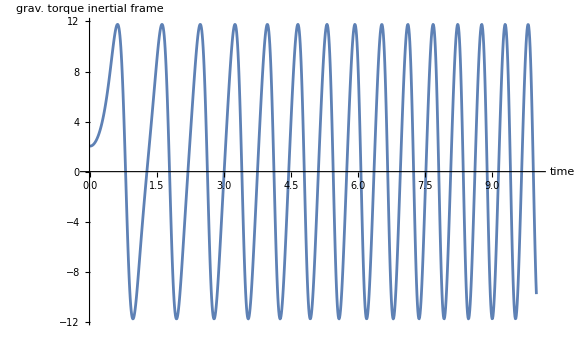

```mathematica
With[{epsilon=0.0001,
(* Adjust here ~~> *)dt=0.01,nMax=1000,
h=1/15.,w=1/4.,vu=3.},
With[{ztxt=6,xtxt=0,ytxt=-2,znl=0.2},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
Ib=rig["moment of inertia"][[1]],Ibi=rig["moment of inertia"][[2]],
cb=rig["cb"],rq0=Q[0,10°,0*-0.5°]},
Module[{rq=rq0,ωb=o,ωs=o,Lb=o,Ls=o,pos=o,ps=o,force=o,τs=o,t=0,
cs=rv[rq0,cb],θv=θvrq[rq0],Στs=o},
Module[{
n=0,tn=ConstantArray[0,nMax],τn=ConstantArray[0,nMax],Στsn=ConstantArray[0,nMax],

ωbLast=ωb,dωbdt=o,dEbrotdt=0,dEbrotdtn=ConstantArray[0,nMax],
Ebrotn=ConstantArray[0,nMax],ΣdtdEbrotdt=0,ΣdtdEbrotdtn=ConstantArray[0,nMax],

ωsLast=ωs,dωsdt=o,dEsrotdt=0,dEsrotdtn=ConstantArray[0,nMax],
Esrotn=ConstantArray[0,nMax],ΣdtdEsrotdt=0,ΣdtdEsrotdtn=ConstantArray[0,nMax]},

For[(n=1;t=0),(n≤nMax),(n++),
τs=((rig["mass"]Abs[g]e3+force)×(cs));
tn[[n]]=t;τn[[n]]=τs;
Στs+=τs*dt;
Στsn[[n]]=Στs;
cs=rv[rq,cb];
{ωb,rq,ωs,Lb,Ls}=oneStepForcedRotationalMotion[ωb,rq,Ib,Ibi,dt,τs];
(* ---------------- energy stats, body frame ---------------- *)
dωbdt=(ωb-ωbLast)/dt;
dEbrotdt=dωbdt.Lb;
dEbrotdtn[[n]]=dEbrotdt;
Ebrotn[[n]]=ωb.Lb/2;
ΣdtdEbrotdt+=(ωb-ωbLast).Lb;
ΣdtdEbrotdtn[[n]]=ΣdtdEbrotdt;
ωbLast=ωb;
(* ---------------- energy stats, space frame ---------------- *)
dωsdt=(ωs-ωsLast)/dt;
dEsrotdt=dωsdt.Lb;
dEsrotdtn[[n]]=dEsrotdt;
Esrotn[[n]]=ωs.Ls/2;
ΣdtdEsrotdt+=(ωs-ωsLast).Ls;
ΣdtdEsrotdtn[[n]]=ΣdtdEsrotdt;
ωsLast=ωs;
(* ------------------------------------------------ *)
t+=dt];
GraphicsColumn[{
ListLinePlot[{{tn,#[[2]]&/@τn}ᵀ},AxesLabel->{"time","grav. torque\ninertial frame"},ImageSize->Large],
ListLinePlot[{{tn,Ebrotn}ᵀ,{tn,ΣdtdEbrotdtn}ᵀ,{tn,dEbrotdtn}ᵀ},PlotLegends->{"body KE","body ∫ⅆKE/ⅆtⅆt","body ⅆKE/ⅆt"},ImageSize->Medium](*,
ListLinePlot[{{tn,Esrotn}ᵀ,{tn,ΣdtdEsrotdtn}ᵀ,{tn,dEsrotdtn}ᵀ}]*)
}]
(*Quiet@ListLinePlot[{{tn,#[[2]]&/@Στsn}ᵀ,{tn,#[[2]]&/@τn}ᵀ}]*)
]]   ]]]
```

The gravitational torque is not qualitatively what we’d expect. It should be zero when the pole is upright or dangling. On a swing-up arc, the torque should go through a “bounce” or “whiplash” as the sliding cart takes some of the lever arm away, thus have two maxima at zenith before falling.

The plots above show steadily increasing angular velocity and kinetic energy, plus a mismatch between kinetic energy and the integral of its derivative, which should always be equal.

But if we decrease ⅆt by a factor of 100 to 100 μsec, we get something much more sensible. It’s visibly not conservative over ten simulated seconds, but it shows the expected torque whiplash, plus the body KE and the integral of its derivative coincide within the resolution of the plot. This takes several minutes to run, so I save only a screenshot.

```mathematica
-Graphics-;
```

Conclusion:

The integrator is guilty.

Because decreasing the time increment results in physically plausible behavior and in better energy conservation, we deem the dynamics correct.

## Discrete Dynamical Integrator

Recast the problem in Lagrangian form. What are good generalized coordinates and velocities? The obvious choice, spherical coordinates, has a singularity at the North pole, right where we want the baton to linger when controlling it. At the North pole, the longitude can be any number. A better choice of coordinates are pitch and cone roll (not axis roll!). These angles are co-latitude δ and an angular displacement η at a clockwise right angle to the great-circle arc of co-latitude. For any non-zero δ, spinning η makes a non-great circle on the surface around a singularity on the Equator. The demonstration below makes this visually clear. Both δ and η are zero and non-singular at the North pole. η has two singularities on the Equator, when δ is 90° or 270°. But that situation is better than a singularity at the North pole because the baton will fly through these poles at the Equator, not linger at them.

The actual physical system is the red ball at the center of mass of the baton, swinging around the origin. The sliding cart is a visual fiction. The Lagrangian, here, does not account for translational energy imparted by the cart, only rotational energy of the baton.

## Demonstration of the Coordinate System

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.,o={0,0,0},thin={0,0,.0001},cb=rig["cb"]},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],s=2,
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}]},
With[{
c3=Cylinder[{o,thin},s cb[[3]]],b3=Sphere[o,s cb[[3]]],
t3x=Tube[{-s cb[[3]] e2,s cb[[3]] e2},.01],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"]},
Manipulate[
DynamicModule[{renderPos=o,Στs=o,cs,rotfn},
cs=RotationMatrix[-η,e1].RotationMatrix[δ,e2].cb;
renderPos=-cs[[1]]e1-cs[[2]]e2;
rotfn=RotationTransform[-η,e1]@*RotationTransform[δ,e2];
Show[{
Graphics3D[{
GeometricTransformation[jack[0],rotfn],
{Black,t3x},
(*{White,Opacity[1./2],Cone[{RotationMatrix[δ,e2].cb,o},1]},*)
{White,Opacity[.7/8],c3,b3,
GeometricTransformation[c3,RotationTransform[δ,e2]]},
{Red,Sphere[s cs,1/16.]},
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],
Translate[
Translate[
GeometricTransformation[rig["graphics primitives"],rotfn],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}],
ParametricPlot3D[s RotationMatrix[-ha,e1].RotationMatrix[δ,e2].cb,{ha,0,2π}]}]],
{{δ,10°},-360°,360°,1°,Appearance->{"Open"}},
{{η,0°},-360°,360°,1°,Appearance->{"Open"}}]]]]
```

## Dynamical Set-Up

### Center of mass

```mathematica
ClearAll[cm];
(cm[{δ_,η_}]:=RotationMatrix[-η,e1].RotationMatrix[δ,e2].{0,0,Subscript[c, z]});
cm[{δ,η}]//MatrixForm
```

(Sin[δ] c_z
Cos[δ] Sin[η] c_z
Cos[δ] Cos[η] c_z)

### z-Height

The potential energy depends only on the z-height of the CM:

```mathematica
ClearAll[zh];
zh[{δ_,η_}]:=-cm[{δ,η}][[3]];
zh[{δ,η}]
```

-Cos[δ] Cos[η] c_z

### Potential Energy

We’ll need symbolical and numerical functions for energy. The symbolical functions support Mathematica’s calculus with parametric functions like δ[t], η[t], δ '[t], and η'[t]. That calculus yields the equations of motion. I learned this technique from Andrew Moylan.[15] The numerical functions support graphics and discrete calculations.

#### numRules

For numerical functions, we replace parametric functions with unbound symbols.

```mathematica
ClearAll[numRules];
numRules={δ[t]->δ,η[t]->η,δ'[t]->Dδ,η'[t]->Dη,m->1,Subscript[c, z]->1.2};
```

```mathematica
ClearAll[Vnum,V];
V[{δ_,η_}]:=m g zh[{δ,η}];V[{δ,η}]
(* Notice not :=, SetDelayed, but =, Set *)
Vnum[{δ_,η_}]=((V[{δ,η}])/.numRules);
Vnum[{δ[t],η[t]}]
```

9.81 m Cos[δ] Cos[η] c_z

11.772 Cos[δ[t]] Cos[η[t]]

### Velocity Vector

The kinetic energy depends on the velocity vector.

```mathematica
ClearAll[v];
(v[{δ_,η_}]:=D[cm[{δ,η}],t]);
v[{δ[t],η[t]}]//FullSimplify//MatrixForm
```

(Cos[δ[t]] c_z δ'[t]
c_z (-Sin[δ[t]] Sin[η[t]] δ'[t]+Cos[δ[t]] Cos[η[t]] η'[t])
-c_z (Cos[η[t]] Sin[δ[t]] δ'[t]+Cos[δ[t]] Sin[η[t]] η'[t]))

### Kinetic Energy

```mathematica
ClearAll[Tnum,T];
(T[{δ_,η_}]:=1/2 m v[{δ,η}].v[{δ,η}]);
T[{δ[t],η[t]}]//FullSimplify
(* hand-constructed, for checking *)
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+Cos[δ]^2 Dη^2);
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+(1/2(1+Cos[2δ]))Dη^2);
(* Set =, not SetDelayed := *)
Tnum[{δ_,η_},{Dδ_,Dη_}]=(T[{δ[t],η[t]}]/.numRules//FullSimplify);
Tnum[{δ,η},{Dδ,Dη}]
```

1/2 m c_z^2 (δ'[t]^2+Cos[δ[t]]^2 η'[t]^2)

0.72 Dδ^2+0.36 Dη^2+0.36 Dη^2 Cos[2 δ]

### Lagrangian

We don’t need Lnum for NDSolve and the equations of motion in this section, but we do need it for the discretized Lagrangian, L_d, later.

```mathematica
ClearAll[Lnum,L];
(L[{δ_,η_}]:=T[{δ,η}]-V[{δ,η}]);L[{δ[t],η[t]}]//FullSimplify
Lnum[{δ_,η_},{Dδ_,Dη_}]:=Tnum[{δ,η},{Dδ,Dη}]-Vnum[{δ,η}];
Lnum[{δ,η},{Dδ,Dη}]
```

0.25 m c_z (-39.24 Cos[δ[t]] Cos[η[t]]+c_z (2. δ'[t]^2+(1.+1. Cos[2 δ[t]]) η'[t]^2))

0.72 Dδ^2+0.36 Dη^2+0.36 Dη^2 Cos[2 δ]-11.772 Cos[δ] Cos[η]

### Leqns

Mathematica has symbolical magic for the Euler-Lagrange equations. See Reference [15].

```mathematica
With[{Lcrds={δ[t],η[t]}},
With[{Lvels=D[Lcrds,t]},
With[{Lncnf={0,0}},(* non-conservative forces *)
Leqns=Flatten@MapThread[
{q,v,f}↦D[D[L[Lcrds],v],t]-D[L[Lcrds],q]==f,
{Lcrds,Lvels,Lncnf}]]]]//FullSimplify
```

{m c_z (-9.81 Cos[η[t]] Sin[δ[t]]+c_z (Cos[δ[t]] Sin[δ[t]] η'[t]^2+δ''[t]))==0,m Cos[δ[t]] c_z (-9.81 Sin[η[t]]+c_z (-2. Sin[δ[t]] δ'[t] η'[t]+Cos[δ[t]] η''[t]))==0}

#### State-Space Form

```mathematica
ClearAll[stEqns];
stEqns=Equal@@@(Solve[Leqns,{δ''[t],η''[t]}]//FullSimplify//Chop//Part[#,1]&)
```

{δ''[t]==Sin[δ[t]] ((9.81 Cos[η[t]])/c_z-1. Cos[δ[t]] η'[t]^2),η''[t]==(9.81 Sec[δ[t]] Sin[η[t]])/c_z+2. Tan[δ[t]] δ'[t] η'[t]}

## Late Discretization: Numerical Solution of Continuous Equations

Solve the system for tLim=25 simulated seconds.

```mathematica
ClearAll[tLim,initialConditions,stSolns];
tLim=25;
initialConditions={δ[0]==10°,η[0]==5°,δ'[0]==0,η'[0]==0};
stSolns=NDSolve[Append[stEqns,initialConditions]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tLim}]
```

{{δ[t]→InterpolatingFunction[…][t],η[t]→InterpolatingFunction[…][t],δ'[t]→InterpolatingFunction[…][t],η'[t]→InterpolatingFunction[…][t]}}

### Plot the Solutions

```mathematica
ClearAll[nsolns];
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},δx,δDotx,ηx,ηDotx,flt},
nsolns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=nsolns[[1,1,2]];δDotx=nsolns[[1,3,2]];ηx=nsolns[[1,2,2]];ηDotx=nsolns[[1,4,2]];
flt="δ_0 = "<>ToString[δ0]<>"°, η_0 = "<>ToString[η0]<>"°";
GraphicsGrid[{
{Plot[δx/°,{t,0,tL},FrameLabel->{{"δ [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[δDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tδ [deg/sec]",""},{"t [sec]",flt}},Frame->True]},
{Plot[ηx/°,{t,0,tL},FrameLabel->{{"η [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[ηDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tη [deg/sec]",""},{"t [sec]",flt}},Frame->True]}}]],
{{δ0,10.°},0.,90.°},{{η0,5.°},0,90.°},{{tL,25},0,50}]
```

### Phase Portrait

Plot the angles versus their velocities, proportional to their Hamiltonian conjugate momenta. If the solution were conservative, these phase portraits would be thin lines. When the time constant is long (400 seconds, here), however, they thicken up, showing that the solution is slightly non-conservative, but it’s much better than our RK4 on Quaternions. This is going to be a good ground-truth.

```mathematica
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},solns,δx,δDotx,ηx,ηDotx},
solns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=solns[[1,1,2]];δDotx=solns[[1,3,2]];ηx=solns[[1,2,2]];ηDotx=solns[[1,4,2]];
ParametricPlot[{{δx,δDotx}/°,{ηx,ηDotx}/°},{t,0,tL},PlotLegends->{"δ","η"}]],
{{δ0,10.°},0,90.°},{{η0,5°},0,90.°},{{tL,400},0,500}]
```

### Ground-Truth Animation

This is pretty convincing. Energy is well conserved. If we were satisfied with an integrator that works only inside Mathematica, we’d be just about done. But we want an integrator we can code up in any programming language.

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.},
With[{ztxt=-1.5,xtxt=0,ytxt=-2,znl=0.3},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
cb=rig["cb"],thin={0,0,.0001},s=2,o={0,0,0}},
With[{c3=Cylinder[{o,thin},s cb[[3]]],b3=Sphere[o,s cb[[3]]],t3x=Tube[{-s cb[[3]] e2,s cb[[3]] e2},.01]},
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},solns,δx,Dδx,ηx,Dηx,flt},
solns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=solns[[1,1,2]];Dδx=solns[[1,3,2]];ηx=solns[[1,2,2]];Dηx=solns[[1,4,2]];
Animate[
Module[{renderPos=o,cs,rotfn},
cs=RotationMatrix[-ηx/.t->u,e1].RotationMatrix[δx/.t->u,e2].cb;
renderPos=-cs[[1]]e1-cs[[2]]e2;
rotfn=RotationTransform[-ηx/.t->u,e1]@*RotationTransform[δx/.t->u,e2];
Show[{Graphics3D[{
Text[font["t = "<>nfm@u<>
", E = "<>nfm@(Tnum[{δx/.t->u,ηx/.t->u},{Dδx/.t->u,Dηx/.t->u}]+Vnum[{δx/.t->u,ηx/.t->u}])],
{xtxt,ytxt,ztxt}],
Text[font["{δ_0,η_0} = "<>vfm@{δ0/°,η0/°}],{xtxt,ytxt,ztxt-znl}],
Text[font["{δ,η} = "<>vfm@{(δx/.t->u)/°,(ηx/.t->u)/°}],{xtxt,ytxt,ztxt-2znl}],
Text[font["c_s = "<>vfm@cs],{xtxt,ytxt,ztxt-3znl}],
{Black,t3x},
{White,Opacity[.7/8],c3,b3,
GeometricTransformation[c3,RotationTransform[δx/.t->u,e2]]},
GeometricTransformation[jack[0],rotfn],
{Red,Sphere[cs,1/16.]},
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],Translate[Translate[
GeometricTransformation[rig["graphics primitives"],rotfn],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}],
ParametricPlot3D[RotationMatrix[-ha,e1].RotationMatrix[δx/.t->u,e2].cb,{ha,0,2π}]}]],
{u,0,tL},AnimationRate->.5]],
{{δ0,10.°},0,90.°},{{η0,5.°},0,90.°},{{tL,25},0,50}]]]]]
```

## Early Discretization

Instead of discretizing the continuous Euler-Lagrange equations, let’s discretize the Lagrangian, itself, via Equation 7 of Reference [10]. First, a reminder:

```mathematica
??Lnum
```

Whereas LNum takes a coordinate tuple q and a velocity tuple q̇, the discrete Lagrangian L_d takes a pair of coordinate tuples: one, q_k, at time t_k and another, q_(k+1), at time t_(k+1). L_d is actually an increment of action (units of energy × time), being the product of a value of LNum (units of energy) and the finite (constant) time increment dt.

```mathematica
ClearAll[Ld,pk,pkp1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,dt];
Ld[qk:{δk_,ηk_},qkp1:{δkp1_,ηkp1_},dt_]:=dt Lnum[1/2(qk+qkp1),1/dt(qkp1-qk)];
```

### Discrete Euler-Lagrange Equations

The discrete Euler-Lagrange equations (DELE), without generalized force terms, are

D_1 L_d(q_k,q_(k+1))+D_2 L_d(q_(k-1),q_k)=0

```mathematica
ClearAll[d1ld,d2ld];
(* Subscript[D, 1] Subscript[L, d](Subscript[q, k],Subscript[q, k+1]) *)
d1ld[{δk_,ηk_},{δkp1_,ηkp1_},dt_]:=
(* {D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δk]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηk]//FullSimplify}, Evaluate in Place *)
{1/dt(-1.44(-δk+δkp1)+5.886 dt^2 Cos[(ηk+ηkp1)/2] Sin[(δk+δkp1)/2]-0.36 (ηk-ηkp1)^2 Sin[δk+δkp1]),
1/dt(0.72ηk-0.72ηkp1+(0.72ηk-0.72ηkp1) Cos[δk+δkp1]+5.886 dt^2 Cos[(δk+δkp1)/2] Sin[(ηk+ηkp1)/2])};
(* +Subscript[D, 2] Subscript[L, d](Subscript[q, k-1],Subscript[q, k]) *)
d2ld[{δkm1_,ηkm1_},{δk_,ηk_},dt_]:=
(* +{D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δkp1]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηkp1]//FullSimplify}, Evaluate in Place *){1/dt(1.44 (δk-δkm1)+5.886 dt^2 Cos[(ηk+ηkm1)/2] Sin[(δk+δkm1)/2]-0.36 (ηk-ηkm1)^2 Sin[δk+δkm1]),1/dt(0.72 ηk-0.72 ηkm1+(0.72 ηk-0.72 ηkm1) Cos[δk+δkm1]+5.886 dt^2 Cos[(δk+δkm1)/2] Sin[(ηk+ηkm1)/2])};
```

### Numerical Solution for δ_1 and η_1

```mathematica
ClearAll[δt,ηt,dt,fh,δ0,η0,δ1,η1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,tn,len,nvars,dsoln];
δt=nsolns[[1,1,2]];ηt=nsolns[[1,2,2]];
dt=1/1000;(* sec *)fh=1.0*dt;
δ0=δt/.{t->0};η0=ηt/.{t->0};
δ1=δt/.{t->dt};η1=ηt/.{t->dt};
tn= 25; (* sec *)
len=tn/dt;
nvars=2;
dsoln=ConstantArray[0,{2nvars,len}];
dsoln[[1,1]]=δ0;dsoln[[2,1]]=η0;
dsoln[[1,2]]=δ1;dsoln[[2,2]]=η1;
Echo@Quiet@AbsoluteTiming@
For[j=2,j<len,j+=1,
Module[{pj,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,r},
δkm1=dsoln[[1,j-1]];ηkm1=dsoln[[2,j-1]];
δk=dsoln[[1,j]];ηk=dsoln[[2,j]];
pj=d1ld[{δk,ηk},{δkp1,ηkp1},dt]+d2ld[{δkm1,ηkm1},{δk,ηk},dt];
r=FindRoot[pj,{{δkp1,δk},{ηkp1,ηk}}];
dsoln[[1;;2,j+1]]=r[[;;,2]];
dsoln[[3;;4,j+1]]=(dsoln[[1;;2,j+1]]-dsoln[[1;;2,j]])/fh;    ]];
```

{7.48801,Null}

```mathematica
ClearAll[TnumFlat,VnumFlat];
TnumFlat[δ_,η_,dδ_,dη_]:=Tnum[{δ,η},{dδ,dη}];
VnumFlat[δ_,η_]:=Vnum[{δ,η}];
```

```mathematica
dδ=dsoln[[1]];
dη=dsoln[[2]];
dδDot=dsoln[[3]];
dηDot=dsoln[[4]];
dT=MapThread[TnumFlat,{dδ,dη,dδDot,dηDot}];
dV=MapThread[VnumFlat,{dδ,dη}];
dE=dT+dV;
mdE=Mean[dE];
nδ=Table[nsolns[[1,1,2]]/.t->u,{u,0dt,24999dt,dt}];
nδDot=Table[nsolns[[1,3,2]]/.t->u,{u,0dt,24999dt,dt}];
nη=Table[nsolns[[1,2,2]]/.t->u,{u,0dt,24999dt,dt}];
nηDot=Table[nsolns[[1,4,2]]/.t->u,{u,0dt,24999dt,dt}];
nT=MapThread[TnumFlat,{nδ,nη,nδDot,nηDot}];
nV=MapThread[VnumFlat,{nδ,nη}];
nE=nT+nV;
mnE=Mean[nE];
```

From the early-discretized solution, we calculate an energy of 11.5490. It slowly drifts upward in the fifth decimal place:

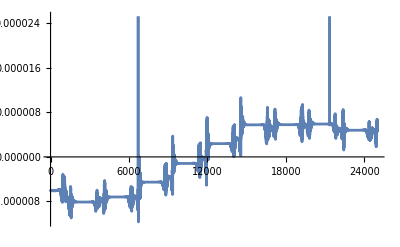

```mathematica
ListLinePlot[nE-mnE]
```

The late-discretized solution has a mean energy of 11.5486+/-0.014, differing from the early-discretized solution in the 5-th figure and with a standard deviation consistent with that difference. It has a periodic error of about that amplitude, and that’s about 2250 times larger than the standard deviation of the energy of the early-discretized solution, 6.2×10^-6. However, the big difference is that the late-discretized solution has no discernible secular (linear) trend, whereas the early-discretized solution, when amplified by 2250, has a visually obvious trend compared to the late-discretized solution.

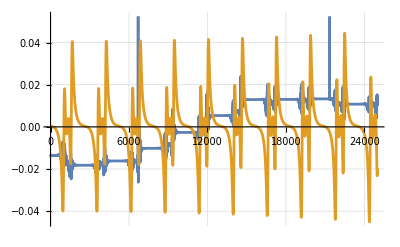

```mathematica
ListLinePlot[{(nE-mnE)*2250,(dE-mdE)},Frame->All,GridLines->Automatic]
```

Eventually, the late-discretized solution would accumulate energy, just like the disastrous quaternion-and-Runge-Kutta solution, and would have to be rebooted. We see, again, that early discretization conserves energy much better than late discretization, though with a much larger periodic error. That periodic error is obviously growing in the plot, and would eventually require a reboot, too, but for a very different reason.

{7.1026,Null}

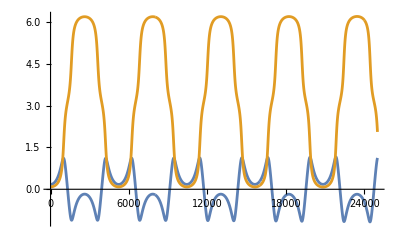

```mathematica
ClearAll[δt,ηt,dt,fh,δ0,η0,δ1,η1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,tn,len,nvars,dsoln];
δt=nsolns[[1,1,2]];ηt=nsolns[[1,2,2]];
dt=1/1000;(* sec *)fh=1.0*dt;
δ0=δt/.{t->0};η0=ηt/.{t->0};
δ1=δt/.{t->dt};η1=ηt/.{t->dt};
tn= 25; (* sec *)
len=tn/dt;
nvars=2;
dsoln=ConstantArray[0,{2nvars,len}];
dsoln[[1,1]]=δ0;dsoln[[2,1]]=η0;
dsoln[[1,2]]=δ1;dsoln[[2,2]]=η1;
Echo@Quiet@AbsoluteTiming@
For[j=2,j<len,j+=1,
Module[{pj,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,r},
δkm1=dsoln[[1,j-1]];ηkm1=dsoln[[2,j-1]];
δk=dsoln[[1,j]];ηk=dsoln[[2,j]];
pj=d1ld[{δk,ηk},{δkp1,ηkp1},dt]+d2ld[{δkm1,ηkm1},{δk,ηk},dt];
r=FindRoot[pj,{{δkp1,δk},{ηkp1,ηk}}];
dsoln[[1;;2,j+1]]=r[[;;,2]];
dsoln[[3;;4,j+1]]=(dsoln[[1;;2,j+1]]-dsoln[[1;;2,j]])/fh;    ]];
ListLinePlot[dsoln[[1;;2,;;]]]
```